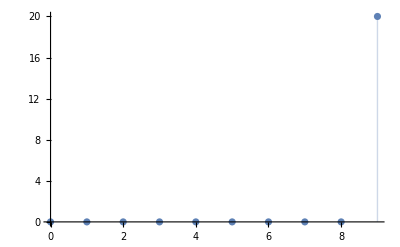

```mathematica
a=1/2;
dx=1/10;
dt=1/100;
m=1/2;

ui=Table[If[i==10,20,0],{i,10}];
uiPlot=Partition[Riffle[Range[0,10],ui],2];
ListPlot[uiPlot,Filling->Axis]
```

Method of Lines Forward Euler

```mathematica
uList={ui};
u=ui;
For[n=1,n≤99,++n,
row={};
For[i=1,i≤10,++i,
If[i==1,
u'=m(u[[i+1]]-2*u[[i]]),(*first position*)
If[i==10,
u'=m(-2*u[[i]]+u[[i-1]]),(*last position*)
u'=m(u[[i+1]]-2*u[[i]]+u[[i-1]])
];
];
un=u+u'*dt;
AppendTo[row,un[[i]]]
];
AppendTo[uList,row];
u=uList[[n]]
];
```

```mathematica
pList=Table[uList[[i]],{i,100}];
ListPlot[{pList[[1]],pList[[50]],pList[[100]]},Filling->Axis,PlotRange->Full,PlotLabel->"Discrete Position & Time Verticals",PlotLabels->{"t=0","t=.5","t=1"}]
```

-Graphics-

Method of Lines Midpoint (not complete)

```mathematica
uList={ui};
m=1/2;
u=ui;
For[n=1,n≤10,++n,
row={};
For[i=1,i≤10,++i,
If[i==1,
un=u[[i]]+m^2/2(u[[i+2]]-3*u[[i+1]]-2*u[[i]]),
If[i==2,
uhalf[x_]=u[[x]]+m/2(u[[x+1]]-2*u[[x]]+u[[x-1]])/.x->i;


AppendTo[row,un]

];
AppendTo[uList,row];
u=uList[[n]]
];
```

Part::pkspec1: The expression x cannot be used as a part specification.

Part::pkspec1: The expression 1+x cannot be used as a part specification.

Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 11 of {«1»} does not exist.

Part::partw: Part 11 of {0,0,0,0,0,0,0,0,0,20} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
N[Simplify[uhalf3[1]]]
```

8.01661×10^-7[1.]